## Model Y

The reaction scheme is as follows :
  
                                                              rib
                                                        ------------ > biomass 
                                                      /       /      \
                                                    /    ATP  ADP
                                                  /
                                                /
        hxt                   gly       /            resp 
glu -------- -> glui --------> pyr       ---------- -> CO2 (not in model)
                               /   \           \          /      \
                        ADP   ATP     \    ADP   ATP
                                                  \
                                                    \
                                                      \ 
                                                        \    ferm
                                                          ------------ > eth


Parameters: Bosdriesz, E., Wortel, M.T., Haanstra, J.R. et al. Low affinity uniporter carrier proteins can increase net substrate uptake rate by reducing efflux. Sci Rep 8, 5576 (2018). https://doi.org/10.1038/s41598-018-23528-7

## General

```mathematica
export = False;
```

```mathematica
exportTest = False;
```

```mathematica
newCalc = False;
```

```mathematica
molWeighEth = 46.06844;
molWeightGlu = 180.1559;
```

```mathematica
0.5*molWeightGlu
```

90.078

```mathematica
dummyVrib = 100;
dummyVribR = {vrib-> dummyVrib};
```

The weight per C-atom in enzymes in dalton, and the other number is the conversion from Dalton to grams and we converted to millimoles since the model is in millimoles.

```mathematica
weightPerCmillimol= 22.35554384671286/1000(**1.66053892*10^(-24)*6.02214129*10^23*)
```

0.0223555

```mathematica
enzConcRealistic = 15*2392.1458333333335
```

35882.2

```mathematica
weightPerCmillimol*enzConcRealistic
```

802.166

```mathematica
ϵ = 0.0001;
```

```mathematica
cm=72/2.54;
```

## Model

Rates: v<reaction name>
Enzymes: e<reaction name>
k_cat’s: kcat<reaction name>
Metabolites: <metabolite name>
Affinity of substrate: km<metabolite name><reaction name>
Inhibition of product (only pyr and eth): ki<metabolite name>
For transport separate rate equation, there kiglui is the “interaction constant”

### Intracell

```mathematica
rates ={
vhxt ->kcathxt  * ehxt((glu[t] - glui[t])/kmgluhxt)/(1+glu[t]/kmgluhxt+glui[t]/kmgluhxt+kiglui(glu[t]/kmgluhxt glui[t]/kmgluhxt)),
vgly -> kcatgly *egly (glui[t]/kmgluigly *adp[t]/kmADPgly)/((glui[t]/kmgluigly*adp[t]/kmADPgly+ glui[t]/kmgluigly + adp[t]/kmADPgly +1)(1+pyr[t]/kipyr)),
vrib -> kcatrib * erib(pyr[t]*atp[t])/(pyr[t]*atp[t]+pyr[t]*kmATPrib+atp[t]*kmpyrrib+kmpyrrib*kmATPrib),
vresp ->kcatresp*eresp (pyr[t]*adp[t])/(pyr[t] adp[t]+pyr[t] kmADPresp+adp[t] kmpyrresp+kmpyrresp kmADPresp)1/(1+Exp[nATP(atp[t]-kIATP)]),
vferm -> kcatferm*eferm pyr[t]/((kmpyrferm+pyr[t])(1+eth[t]/kieth))1/(1+Exp[nATP(atp[t]-kIATP)])
}/.adp[t] -> (concAXP-atp[t]);
```

```mathematica
ratesBiom = Join[rates, {vbms-> Subscript[s, bmpyr] vrib}];
```

```mathematica
odesIn = {
glui'[t] ==  Subscript[s, glui,hxt] vhxt + Subscript[s, glui,gly] vgly,
pyr'[t]   ==  Subscript[s, pyr,gly] vgly +Subscript[s, pyr,rib] vrib+ Subscript[s, pyr,ferm] vferm + Subscript[s, pyr,resp] vresp,
atp'[t]   ==  Subscript[s, atp,hxt] vhxt + Subscript[s, atp,gly] vgly +Subscript[s, atp,resp] vresp+ Subscript[s, atp,rib] vrib
};
```

-Graphics-

-Graphics-

```mathematica
stoichFix = {
Subscript[s, glui,hxt]-> 1,
Subscript[s, glui,gly]->-1,
Subscript[s, pyr,gly]-> 2,
Subscript[s, pyr,resp]-> -1,
Subscript[s, pyr,ferm]-> -1,
Subscript[s, atp,hxt]-> 0,
Subscript[s, atp,gly]->  2,
Subscript[s, bmpyr]-> 3
};
stoichLit= {
Subscript[s, pyr,rib]-> -1,
Subscript[s, atp,rib]-> -2.4,
Subscript[s, atp,resp] -> 9
};
stoich = Join[stoichFix, stoichLit];
```

```mathematica
ratesBiomS = {vbms-> Subscript[s, bmpyr] vrib}/. stoich/.dummyVribR;
```

-Graphics-

```mathematica
kcats = {
kcathxt -> 13.298,
kcatresp->0.051,
kcatrib->0.639,
kcatferm ->8.321,
kcatgly -> 1.804
};
```

-Graphics-

-Graphics-

```mathematica
kms = {
kmgluhxt -> 1.19,
kmpyrresp->0.13, (* Calc *)
kmpyrrib->1,
kmpyrferm-> 6,  (* Calc - Joep: 0.8533 (hill equation 3.5772) *)
kmgluigly -> 0.08, (* Calc - Joep: 0.2021 *)
kmADPgly -> 1,
kmADPresp -> 1,
kmATPrib -> 1,
kIATP-> 2.,
nATP->5
};
kis = {
kieth ->17, (* Calc *)
kipyr -> 21, (* Calc *)
kiglui -> 0.91 (* Calc *)
};
otherparam = {
concAXP -> 3.1  (* Calc *)
};
kineticparam = Join[kcats, kms, kis, otherparam];
```

```mathematica
kcats// TableForm
```

kcathxt→13.298
kcatresp→0.051
kcatrib→0.639
kcatferm→8.321
kcatgly→1.804

```mathematica
paramtest = Join[stoich, kineticparam, kcats]/. Subscript[x___]:> Symbol[StringJoin[SymbolName/@List[x]]]
```

{sgluihxt→1,sgluigly→-1,spyrgly→2,spyrresp→-1,spyrferm→-1,satphxt→0,satpgly→2,sbmpyr→3,spyrrib→-1,satprib→-2.4,satpresp→9,kcathxt→13.298,kcatresp→0.051,kcatrib→0.639,kcatferm→8.321,kcatgly→1.804,kmgluhxt→1.19,kmpyrresp→0.13,kmpyrrib→1,kmpyrferm→6,kmgluigly→0.08,kmADPgly→1,kmADPresp→1,kmATPrib→1,kIATP→2.,nATP→5,kieth→17,kipyr→21,kiglui→0.91,concAXP→3.1,kcathxt→13.298,kcatresp→0.051,kcatrib→0.639,kcatferm→8.321,kcatgly→1.804}

```mathematica
concmet = {atp, pyr, glui};
concenzym = {ehxt,egly,erib,eresp,eferm};
```

```mathematica
constraints = {
0< glui <  glu,
0 < atp < concAXP,
0< pyr
};
```

```mathematica
ssIntracell=Thread[odesIn⟦All,2⟧==0]/. stoich;
```

```mathematica
yieldsMu = {mu-> vbms/Total[concenzym],yieldXS->  vbms/vhxt weightPerCmillimol,yieldEtOHX-> vferm/vbms 1/weightPerCmillimol, yieldEtOHS ->vferm/vhxt };
```

```mathematica
ssIn[enz_List,s_?NumericQ, p_?NumericQ]:= Module[{timesol, init,ssSol},
timesol=NDSolve[Join[odesIn/. stoich/.rates/. {glu[t]-> s, eth[t]-> p} /. kineticparam /. enz, {glui[0]== s/2, pyr[0]== s, atp[0]== 1}], concmet, {t, 0, 100}]⟦1⟧;(* Time simulation *)
init={#, #[t]/.timesol /. t-> 100}&/@concmet ;(* Values from the time simulation are used as initial values for the optimization *)
ssSol=FindRoot[Join[ssIntracell /.rates /. x_[t]:> x]/. {glu-> s, eth-> p} /. kineticparam/. enz, init ];
yieldsMu//. ratesBiom /. stoich/. kineticparam/.enz/. x_[t]:> x/. {glu-> s, eth-> p} /. ssSol
]
```

```mathematica
ssIn::usage= "ssIn[enzList, glu, eth] (internal SS) gives mu, yield X/S and yield EtOH/S";
```

```mathematica
ssIn[{ehxt-> 1, egly-> 1, eresp-> 0, eferm-> .01, erib-> 1}, 10, 0]
```

{mu→0.0583137,yieldXS→0.0558889,yieldEtOHX→20.8748,yieldEtOHS→1.16667}

```mathematica
growth[enz_List,s_?NumericQ, p_?NumericQ]:= mu/.ssIn[enz,s, p]
biomassYield[enz_List,s_?NumericQ, p_?NumericQ]:= yieldXS/.ssIn[enz,s, p]
ethanolYield[enz_List,s_?NumericQ, p_?NumericQ]:= yieldEtOHX/.ssIn[enz,s, p]
```

```mathematica
growth::usage= "growth[enzList, glu, eth] gives the specific growth rate (uses ssIn)";
biomassYield::usage= "ssIn[enzList, glu, eth] gives the yield X/S in gram per millimole (uses ssIn)";
ethanolYield::usage= "ssIn[enzList, glu, eth] gives the yield EtOH/X in millimole per gram (uses ssIn)";
```

### Optimization

```mathematica
ClearAll[ratesFerm,ratesResp,ratesMix, enzFerm, enzResp, totenzFerm, totenzResp, totenzMix]
ratesMix[fracResp_,ribrate_]:=Module[{rat,solTMP, rfTot},
rat=Solve[{vresp/(vresp+vferm)==fracResp,vresp+vferm==rfTot},{vresp,vferm}]//Flatten;
solTMP=Solve[ssIntracell/.rat/.vrib->ribrate];
Thread[rates⟦All,1⟧-> Flatten[(rates⟦All,1⟧/.rat/.solTMP/.vrib->ribrate)]]
]
ratesFerm[ribrate_]:=Solve[ssIntracell /. vresp-> 0/. vrib-> ribrate, {vhxt,vgly,vferm}]⟦1⟧~Join~{vresp-> 0,vrib-> ribrate}
ratesResp[ribrate_]:=Solve[ssIntracell /. vferm-> 0 /. vrib-> ribrate, {vhxt,vgly,vresp}]⟦1⟧~Join~{vferm-> 0,vrib-> ribrate}
enzFerm[ribrate_,glucose_,ethanol_, met_] := Thread[Rule[concenzym,concenzym/. Solve[Equal@@@rates, concenzym]⟦1⟧/. ratesFerm[ribrate]/. kineticparam/. x_[t]:> x /. glu-> glucose /. eth-> ethanol/.met]]
enzResp[ribrate_, glucose_, met_] := Thread[Rule[concenzym,concenzym/. Solve[Equal@@@rates, concenzym]⟦1⟧/. ratesResp[ribrate]/. kineticparam /. x_[t]:> x/. eth-> 0/. glu-> glucose/.met]]
totenzFerm[ribrate_] := Total[concenzym]/. Solve[Equal@@@rates, concenzym]⟦1⟧/. ratesFerm[ribrate]/. kineticparam/. x_[t]:> x
totenzResp[ribrate_] := Total[concenzym]/. Solve[Equal@@@rates, concenzym]⟦1⟧/. ratesResp[ribrate]/. kineticparam /. x_[t]:> x/. eth-> 0
totenzMix[Q_,ribrate_]:=Total[concenzym]/.Flatten[Solve[Equal@@@rates,concenzym]]/.ratesMix[Q,ribrate]/.kineticparam/.x_[t]->x
enzFerm::usage="enzFerm[ribrate_,glucose_,ethanol_, met_] gives a replacement list for the enzyme concentrations";
enzResp::usage="enzFerm[ribrate_,glucose_,met_] gives a replacement list for the enzyme concentrations";
```

```mathematica
ClearAll[runFerm,runResp,runMix]
runFerm[newS_?NumericQ, newEth_?NumericQ, ribrate_]:= NMinimize[{totenzFerm[ribrate]/.glu-> newS/. eth-> newEth}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < newS - ϵ}/. kineticparam, concmet]
runResp[newS_?NumericQ, ribrate_]:= NMinimize[{totenzResp[ribrate] /. glu-> newS}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < newS - ϵ}/. kineticparam, concmet]
runMix[Q_?NumericQ,newS_?NumericQ,newEth_?NumericQ,ribrate_]:=NMinimize[{totenzMix[Q,ribrate]/.glu-> newS/. eth-> newEth}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < newS - ϵ}/. kineticparam, concmet]
runFerm::usage= "runFerm[glu, eth, ribrate] gives the total enzyme and internal metabolite concentrations of the fermentor for a vrib of ribrate for fixed glu and eth concentrations";
runResp::usage= "runFerm[glu, ribrate] gives the total enzyme and internal metabolite concentrations of the respirer for a vrib of ribrate for fixed glu concentrations";
runMix::usage= "runMix[Q,glu,eth, ribrate] gives the total enzyme and internal metabolite concentrations of a mixed strategy for a vrib of ribrate for fixed glu concentrations. Q gives v_resp/v_rib";
```

```mathematica
ClearAll[growthRateFerm,growthRateResp,growthRateMix]
growthRateFerm[s_?NumericQ, newEth_?NumericQ]:= (vbms /.ratesBiomS)/NMinimize[{totenzFerm[dummyVrib]/.glu->s/. eth-> newEth}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < s - ϵ}/. kineticparam, concmet]⟦1⟧
growthRateResp[s_?NumericQ]:= (vbms /.ratesBiomS)/NMinimize[{totenzResp[dummyVrib]/.glu->s}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < s - ϵ}/. kineticparam, concmet]⟦1⟧
growthRateMix[ratio_?NumericQ,s_?NumericQ, newEth_?NumericQ]:= (vbms /.ratesBiomS)/NMinimize[{totenzMix[ratio, dummyVrib]/.glu->s/. eth-> newEth}~Join~{ϵ< pyr, ϵ < atp < concAXP-ϵ, ϵ <glui < s - ϵ}/. kineticparam, concmet]⟦1⟧
```

```mathematica
growthRateFerm::usage= "growthRateFerm[glu, eth] gives the optimal specific growth rate of the fermentor (needed for some minimization functions) for fixed glu and eth concentrations";
growthRateResp::usage= "growthRateResp[glu] gives the optimal specific growth rate of the respirer (needed for some minimization functions) for fixed glu and eth concentrations";
growthRateMix::usage= "growthMix[ratio, glu, eth] gives the optimal specific growth rate of a mixed strategy (needed for some minimization functions) for fixed glu and eth concentrations";
```

```mathematica
runFerm[1000, 0, dummyVrib]
```

{500.007,{atp→1.62193,pyr→8.09854,glui→1.33493}}

```mathematica
Solve[Equal@@@rates, concenzym]⟦1⟧ /. x_[t]-> x/. kineticparam/. glu-> 1000/. eth-> 0/.runFerm[1000, 0, dummyVrib]⟦2⟧/. ratesFerm[.1]
```

{ehxt→0.018283,egly→0.163791,erib→0.284219,eresp→0.,eferm→0.0337134}

```mathematica
Solve[Equal@@@rates, concenzym]⟦1⟧ /. x_[t]-> x/. kineticparam/. glu-> 1/. eth-> 0/.runResp[1, dummyVrib]⟦2⟧/. ratesResp[.1]
```

{ehxt→0.0193663,egly→0.0892874,erib→0.316326,eresp→0.428208,eferm→0.}

```mathematica
yieldsResp = {yieldXS->  (yieldXS/. yieldsMu),yieldEtOHX-> (yieldEtOHX/. yieldsMu), yieldEtOHS-> (yieldEtOHS/. yieldsMu)} /. ratesBiomS/. ratesResp[dummyVrib];
yieldsFerm = {yieldXS->  (yieldXS/. yieldsMu),yieldEtOHX-> (yieldEtOHX/. yieldsMu), yieldEtOHS-> (yieldEtOHS/. yieldsMu)} /. ratesBiomS/. ratesFerm[dummyVrib];
yieldsBoth = Join[yieldsResp /. Rule[a_, b_]:> Rule[a[1], b], yieldsFerm /. Rule[a_, b_]:> Rule[a[2], b]];
yieldsMix[RATIO_]:={yieldXS->  (yieldXS/. yieldsMu),yieldEtOHX-> (yieldEtOHX/. yieldsMu)} /. ratesBiomS/. ratesMix[RATIO,dummyVrib]
```

```mathematica
(1000/glucoseGramPerMole) *yieldXS /. yieldsResp
```

117.661/glucoseGramPerMole

```mathematica
(1000/glucoseGramPerMole) *yieldXS /. yieldsFerm
```

55.8889/glucoseGramPerMole

## Calculate trade-off curve

### Model Simulations for fixed glu en eth concentrations

```mathematica
startS = .001;
```

```mathematica
If[newCalc, vergRespFerm={Table[{runFerm[startS 2^s, 100., dummyVrib], startS 2^s}, {s, 1, 14, .1}], Table[{runFerm[startS 2^s, 0., dummyVrib], startS 2^s}, {s, 1, 14, .1}],Table[{runResp[startS 2^s, dummyVrib], startS 2^s}, {s, 1, 14,.1}]}];
```

```mathematica
If[newCalc, DeleteFile[FileNameJoin[{NotebookDirectory[], "data", "vergRespFerm"}]];  Save[FileNameJoin[{NotebookDirectory[], "data", "vergRespFerm"}], vergRespFerm]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "data", "vergRespFerm"}]];
```

```mathematica
vergRespFermResSub = vergRespFerm /. {sol_List, s_Real}:> {vbms/sol⟦1⟧, s}/. ratesBiomS;
```

```mathematica
vergRespFermYield = {vergRespFerm⟦1⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧,vbms/vhxt/. ratesFerm[dummyVrib]},
vergRespFerm⟦2⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧,vbms/vhxt/. ratesFerm[dummyVrib]},vergRespFerm⟦3⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧,vbms/vhxt/. ratesResp[dummyVrib]}}/. ratesBiomS;
```

```mathematica
vergRespFermPyr = vergRespFerm /. {sol_List, _Real}:> {vbms/sol⟦1⟧, pyr /. sol⟦2⟧}/. ratesBiomS;
```

```mathematica
vergRespFermqCO2 = {vergRespFerm⟦1⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, (2 vferm+ 6 vresp) enzConcRealistic/sol⟦1⟧0.002/. ratesFerm[dummyVrib]},
vergRespFerm⟦2⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, (2 vferm+ 6 vresp) enzConcRealistic/sol⟦1⟧0.002/. ratesFerm[dummyVrib]},vergRespFerm⟦3⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, (2 vferm+ 6 vresp) enzConcRealistic/sol⟦1⟧0.002/. ratesResp[dummyVrib]}}/. ratesBiomS;
```

```mathematica
vergRespFermqO2 = {vergRespFerm⟦1⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, 6 vresp enzConcRealistic/sol⟦1⟧0.002/. ratesFerm[dummyVrib]},
vergRespFerm⟦2⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, 6 vresp enzConcRealistic/sol⟦1⟧0.002/. ratesFerm[dummyVrib]},vergRespFerm⟦3⟧ /. {sol_List, _Real}:> {vbms/sol⟦1⟧, 6 vresp enzConcRealistic/sol⟦1⟧0.002/. ratesResp[dummyVrib]}}/. ratesBiomS;
```

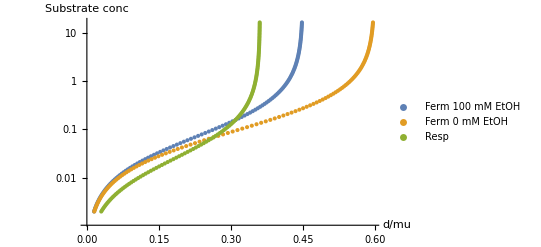

```mathematica
growtStrains =ListLogPlot[{vergRespFermResSub⟦1⟧, vergRespFermResSub⟦2⟧,vergRespFermResSub⟦3⟧}(*, PlotRange-> {0, 0.35}*), PlotLegends->{"Ferm 100 mM EtOH", "Ferm 0 mM EtOH", "Resp"}, AxesLabel->{"d/mu", "Substrate conc"}]
```

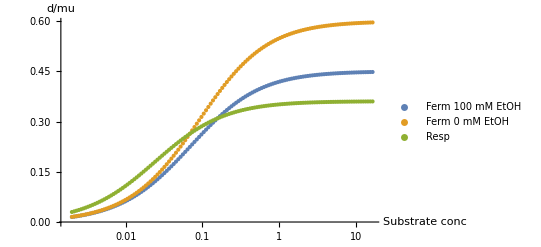

```mathematica
growtStrainsReverse =ListLogLinearPlot[{Reverse/@vergRespFermResSub⟦1⟧, Reverse/@vergRespFermResSub⟦2⟧,Reverse/@vergRespFermResSub⟦3⟧}(*, PlotRange-> {0, 0.35}*), PlotLegends->{"Ferm 100 mM EtOH", "Ferm 0 mM EtOH", "Resp"}, AxesLabel->{"Substrate conc", "d/mu"}]
```

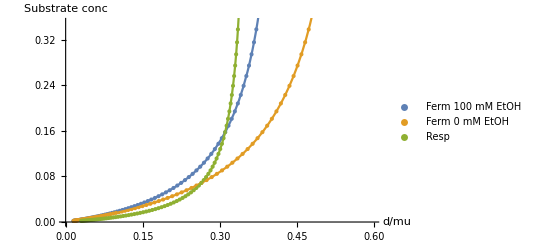

```mathematica
(*check if interpolation is decent*)
Show[ListPlot[{vergRespFermResSub⟦1⟧, vergRespFermResSub⟦2⟧,vergRespFermResSub⟦3⟧}, PlotRange-> {0, 0.35}, PlotLegends->{"Ferm 100 mM EtOH", "Ferm 0 mM EtOH", "Resp"}, AxesLabel->{"d/mu", "Substrate conc"}],Plot[{Interpolation[vergRespFermResSub⟦1⟧][x], Interpolation[vergRespFermResSub⟦2⟧][x], Interpolation[vergRespFermResSub⟦3⟧][x]}, {x, 0.1, 0.5}]]
```

### Find μ_max and K_M of the different strains

#### Calculate intersection of respiring and fermenting strains and select best strain for each substrate concentration

```mathematica
diffRespFerm=Partition[Sort[Reverse/@Flatten[vergRespFermResSub[[2;;3]],1]],2]/. {{sub_,mu_}, {sub2_,mu2_}}:> {sub, Abs[mu-mu2]};
```

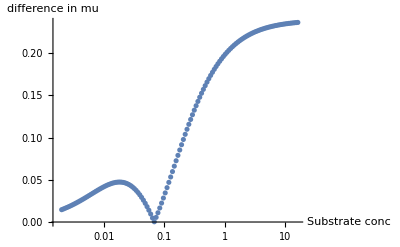

```mathematica
ListLogLinearPlot[diffRespFerm,AxesLabel->{"Substrate conc","difference in mu"}]
```

```mathematica
intersection = diffRespFerm[[Position[diffRespFerm,Min[diffRespFerm]]⟦1,1⟧]]
```

{0.0685935,0.00027259}

```mathematica
Position[vergRespFermResSub⟦2⟧, intersection⟦1⟧]
```

{{52,2}}

```mathematica
vergRespFermResSub⟦2, 52⟧
vergRespFermResSub⟦3, 52⟧
```

{0.264074,0.0685935}

{0.263801,0.0685935}

```mathematica
bestStrainsRate = Join[vergRespFermResSub[[3, 1;;52]], vergRespFermResSub[[2, 53;;]]];
```

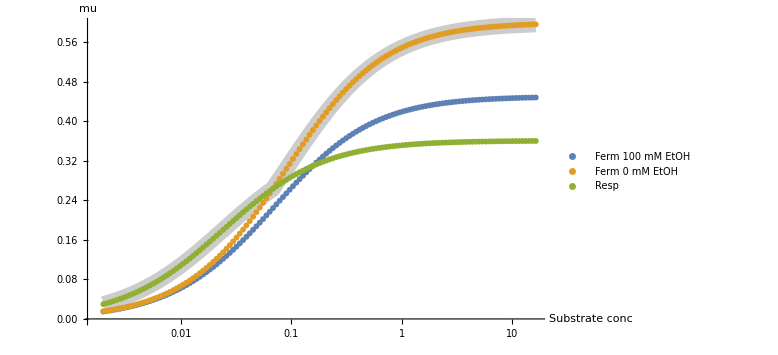

```mathematica
Show[ListLogLinearPlot[Reverse/@bestStrainsRate, AxesLabel->{"Substrate conc","mu"}, Joined-> True, PlotStyle-> {GrayLevel[.8],Thickness[.02]},ImageSize->Large], growtStrainsReverse]
```

```mathematica
bestStrains=Join[vergRespFerm[[3, 1;;52]], vergRespFerm[[2, 53;;]]];
```

#### Make a growth curve of one of the strains: From 1-52 are resp 53-131 are ferm

```mathematica
bestStrains⟦1⟧
bestStrains⟦-1⟧
```

{{10008.4,{atp→0.680072,pyr→1.53524,glui→0.000927877}},0.002}

{{502.838,{atp→1.62052,pyr→8.06366,glui→1.15177}},16.384}

```mathematica
?ssIn
```

ssIn[enzList, glu, eth] (internal SS) gives mu, yield X/S and yield EtOH/S

```mathematica
growthCurveFerm[{{totenz_,metopt_},subopt_}] :=Table[{startS 2^s,growth[enzFerm[dummyVrib, subopt,0,metopt],startS 2^s,0]},{s, 1, 14, .1}];
growthCurveResp[{{totenz_,metopt_},subopt_}] :=Table[{startS 2^s,growth[enzResp[dummyVrib, subopt,metopt],startS 2^s,0]},{s, 1, 14, .1}]
```

```mathematica
enzResp[dummyVrib, bestStrains⟦10,2⟧,0,bestStrains⟦10,1,2⟧]
```

enzResp[100,0.00373213,0,{atp→0.800114,pyr→1.99817,glui→0.00174661}]

```mathematica
enzFerm[dummyVrib, bestStrains⟦-1,2⟧,bestStrains⟦-1,1,2⟧]
```

enzFerm[100,16.384,{atp→1.62052,pyr→8.06366,glui→1.15177}]

```mathematica
ssIn[enzResp[dummyVrib, bestStrains⟦10,2⟧,bestStrains⟦10,1,2⟧],startS 2^1,0]
ssIn[enzResp[dummyVrib, bestStrains⟦10,2⟧,bestStrains⟦10,1,2⟧],startS 2^14,0]
ssIn[enzFerm[dummyVrib, bestStrains⟦-1,2⟧, 0,bestStrains⟦-1,1,2⟧],startS 2^1, 0]
ssIn[enzFerm[dummyVrib, bestStrains⟦-1,2⟧, 0,bestStrains⟦-1,1,2⟧],startS 2^14, 0]
```

{mu→0.0262653,yieldXS→0.117661,yieldEtOHX→0.,yieldEtOHS→0.}

{mu→0.0567375,yieldXS→0.117661,yieldEtOHX→0.,yieldEtOHS→0.}

{mu→0.0020181,yieldXS→0.0558889,yieldEtOHX→20.8748,yieldEtOHS→1.16667}

{mu→0.596614,yieldXS→0.0558889,yieldEtOHX→20.8748,yieldEtOHS→1.16667}

```mathematica
If[newCalc, allGrowthCurves = Join[growthCurveResp/@bestStrains⟦1;;52⟧,growthCurveFerm/@bestStrains⟦53;;⟧]];
```

```mathematica
If[newCalc, DeleteFile[FileNameJoin[{NotebookDirectory[], "data", "allGrowthCurves"}]];  Save[FileNameJoin[{NotebookDirectory[], "data", "allGrowthCurves"}], allGrowthCurves]]
```

```mathematica
Get[FileNameJoin[{NotebookDirectory[], "data", "allGrowthCurves"}]];
```

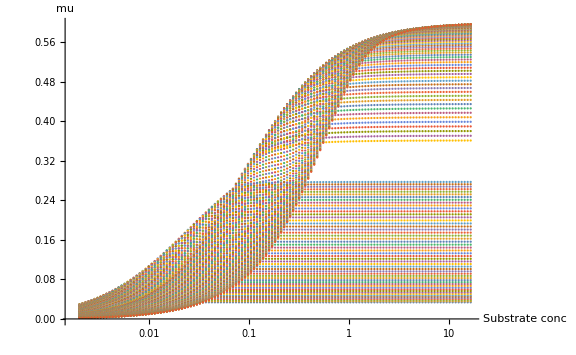

```mathematica
ListLogLinearPlot[allGrowthCurves, AxesLabel->{"Substrate conc", "mu"}, PlotRange->All, ImageSize->Large]
```

```mathematica
fitWithHill[growthCurve_]:= Module[{mumaxtry = Max[growthCurve⟦All,2⟧], kmtry ,htry=1,mumaxL,kmL,sL,hL},
kmtry= growthCurve⟦Ordering[Abs[growthCurve⟦All,2⟧-1/2mumaxtry],1]⟦1⟧⟧⟦1⟧;
fit=NonlinearModelFit[growthCurve, mumaxL sL^hL/(sL^hL+kmL^hL), {{mumaxL,mumaxtry},{ kmL, kmtry},{hL,1}},sL];
fit/.{mumaxL->mumax, kmL->km, hL-> h, sL-> s}
]
```

```mathematica
allFits=fitWithHill/@allGrowthCurves;
```

NonlinearModelFit::nrlnum: The function value {-0.00261327-0.0312143 ⅈ,-0.00260112-0.0302085 ⅈ,-0.00207037-0.029106 ⅈ,-0.00120519-0.027932 ⅈ,-0.000273339-0.0267102 ⅈ,«42»,0.00163522-0.00226373 ⅈ,0.00156708-0.0021464 ⅈ,0.00150178-0.00203554 ⅈ,«81»} is not a list of real numbers with dimensions {131} at {mumaxL$16559,kmL$16559,hL$16559} = {0.0337624,-0.00137558,0.706525}.

NonlinearModelFit::nrlnum: The function value {0.00844993-0.0361472 ⅈ,0.00798355-0.0339556 ⅈ,0.00762967-0.031759 ⅈ,0.00769968-0.0296025 ⅈ,0.00802245-0.0275193 ⅈ,«42»,0.00160959-0.00151778 ⅈ,0.00153122-0.00143338 ⅈ,0.00145687-0.00135398 ⅈ,«81»} is not a list of real numbers with dimensions {131} at {mumaxL$16568,kmL$16568,hL$16568} = {0.0357891,-0.00122615,0.76255}.

NonlinearModelFit::nrlnum: The function value {0.0281981-0.0322131 ⅈ,0.0255834-0.0286368 ⅈ,0.0228212-0.025491 ⅈ,0.0203723-0.0227346 ⅈ,0.0185824-0.020323 ⅈ,«42»,0.00129765-0.000744825 ⅈ,0.00122441-0.000700221 ⅈ,0.00115547-0.000658431 ⅈ,«81»} is not a list of real numbers with dimensions {131} at {mumaxL$16577,kmL$16577,hL$16577} = {0.0379081,-0.00102595,0.836677}.

General::stop: Further output of NonlinearModelFit::nrlnum will be suppressed during this calculation.

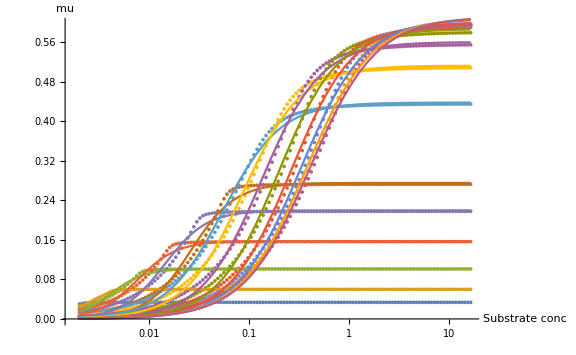

```mathematica
every=10;
Show[ListLogLinearPlot[allGrowthCurves⟦;; ;; every⟧, AxesLabel->{"Substrate conc", "mu"}, PlotRange->All, ImageSize->Large],LogLinearPlot[Evaluate[#[s]&/@allFits⟦;; ;; every⟧], {s,startS 2^1, startS 2^14}, PlotRange->All]]
```

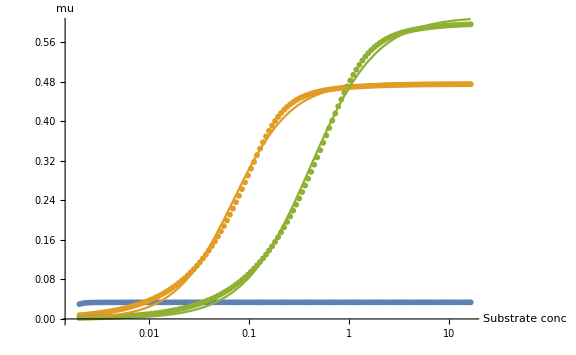

```mathematica
every=65;
Show[ListLogLinearPlot[allGrowthCurves⟦;; ;; every⟧, AxesLabel->{"Substrate conc", "mu"}, PlotRange->All, ImageSize->Large],LogLinearPlot[Evaluate[#[s]&/@allFits⟦;; ;; every⟧], {s,startS 2^1, startS 2^14}, PlotRange->All]]
```

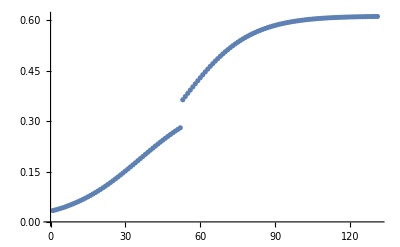
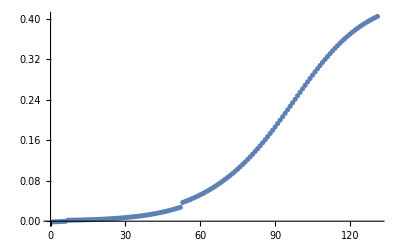
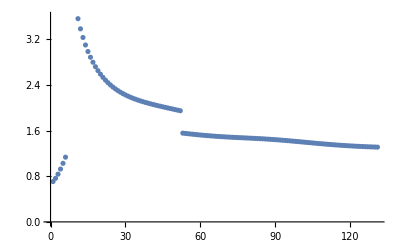

```mathematica
{ListPlot[mumax/. #["BestFitParameters"]&/@allFits], ListPlot[km/. #["BestFitParameters"]&/@allFits], ListPlot[h/. #["BestFitParameters"]&/@allFits]}
```

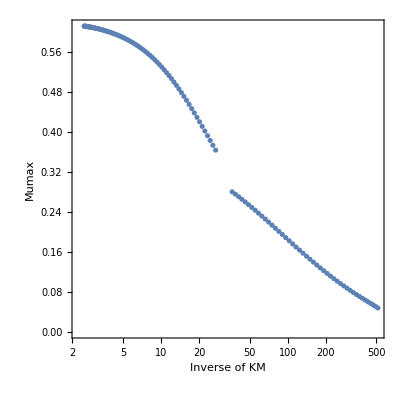

```mathematica
ListLogLinearPlot[{1/km,mumax}/. #["BestFitParameters"]&/@allFits, Frame-> True, AspectRatio->1, FrameLabel->{"Inverse of KM", "Mumax"}, BaseStyle->{"Arial",14}]
```

```mathematica
tradeOffData={km,mumax}/. #["BestFitParameters"]&/@allFits;
```

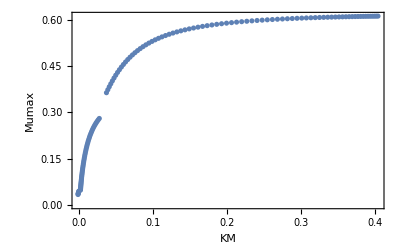

```mathematica
ListPlot[tradeOffData, Frame-> True, FrameLabel->{"KM", "Mumax"}, BaseStyle->{"Arial",14}, PlotRange->All]
```

```mathematica
tradeOffFit=NonlinearModelFit[tradeOffData, {maxmu km/(kref+km), maxmu>0,kref>0}, {{maxmu,0.6}, {kref,0.2}},km]
```

FittedModel[(0.665121 km)/(0.0282249+km)]

```mathematica
mumaxYeast[k_]:=(0.67 k)/(0.028+k)
```

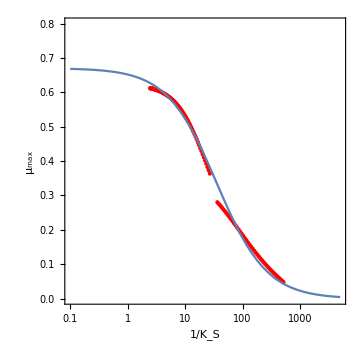

```mathematica
Show[ListLogLinearPlot[{tradeOffData/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/K_S", "μ_max"}, AspectRatio->1, PlotStyle-> {{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{.1, 5000},{0,0.8}}], LogLinearPlot[mumaxYeast[1/x], {x, .1, 5000}]]
```

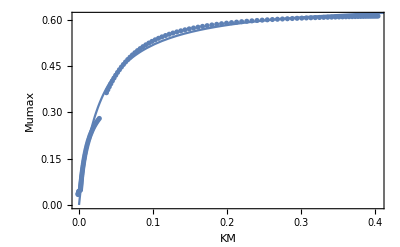

```mathematica
Show[ListPlot[tradeOffData, Frame-> True, FrameLabel->{"KM", "Mumax"}, BaseStyle->{"Arial",14}],Plot[tradeOffFit[km], {km, 0,0.5}, Frame-> True, PlotRange->All]]
```

### Anaerobic

```mathematica
growthCurvesFerm = growthCurveFerm/@vergRespFerm[[2]][[1;;-1;;5]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

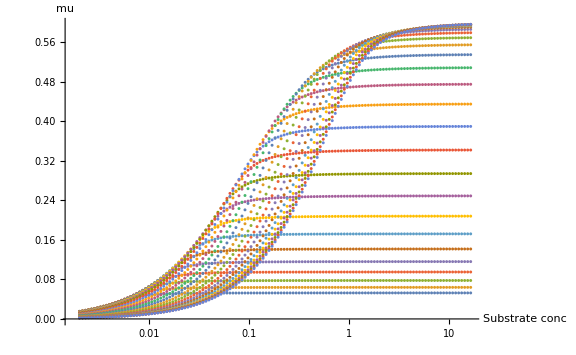

```mathematica
ListLogLinearPlot[growthCurvesFerm, AxesLabel->{"Substrate conc", "mu"}, PlotRange->All, ImageSize->Large]
```

```mathematica
allFitsFerm=fitWithHill/@growthCurvesFerm;
```

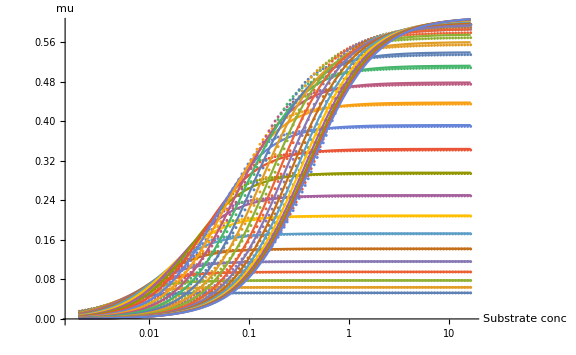

```mathematica
Show[ListLogLinearPlot[growthCurvesFerm, AxesLabel->{"Substrate conc", "mu"}, PlotRange->All, ImageSize->Large],LogLinearPlot[Evaluate[#[s]&/@allFitsFerm], {s,startS 2^1, startS 2^14}, PlotRange->All]]
```

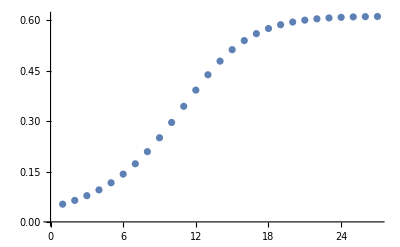
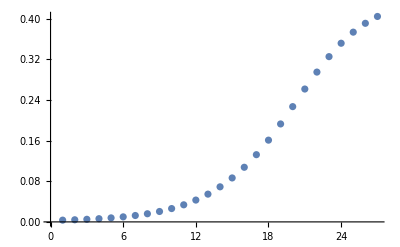
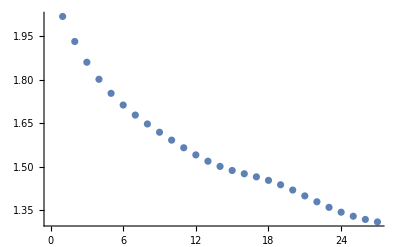

```mathematica
{ListPlot[mumax/. #["BestFitParameters"]&/@allFitsFerm], ListPlot[km/. #["BestFitParameters"]&/@allFitsFerm], ListPlot[h/. #["BestFitParameters"]&/@allFitsFerm]}
```

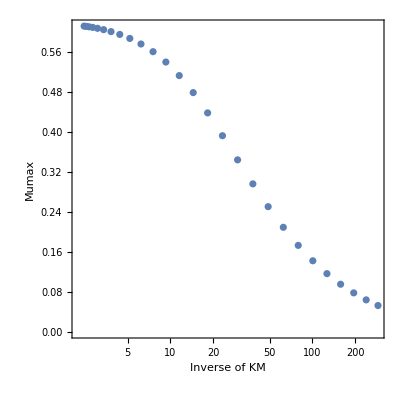

```mathematica
ListLogLinearPlot[{1/km,mumax}/. #["BestFitParameters"]&/@allFitsFerm, Frame-> True, AspectRatio->1, FrameLabel->{"Inverse of KM", "Mumax"}, BaseStyle->{"Arial",14}]
```

Compare with aerobic case

-Graphics-

```mathematica
tradeOffDataFerm={km,mumax}/. #["BestFitParameters"]&/@allFitsFerm;
```

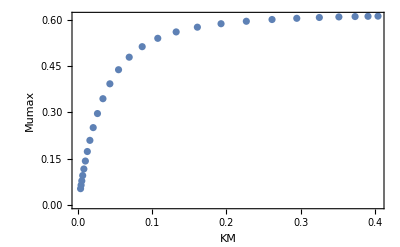

```mathematica
ListPlot[tradeOffDataFerm, Frame-> True, FrameLabel->{"KM", "Mumax"}, BaseStyle->{"Arial",14}, PlotRange->All]
```

```mathematica
tradeOffFitFerm=NonlinearModelFit[tradeOffDataFerm, {maxmu km/(kref+km), maxmu>0,kref>0}, {{maxmu,0.6}, {kref,0.2}},km]
```

FittedModel[(0.679605 km)/(0.0331379+km)]

```mathematica
mumaxYeastFerm[k_]:=(0.68 k)/(0.033+k)
```

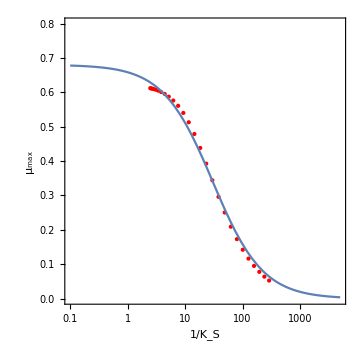

```mathematica
Show[ListLogLinearPlot[{tradeOffDataFerm/. {k_, mu_}:> {1/k, mu}}, Frame -> True,FrameLabel->{"1/K_S", "μ_max"}, AspectRatio->1, PlotStyle-> {{PointSize[Medium], Red}}, BaseStyle->{16,FontFamily->"Arial"}, ImageSize->Medium, PlotRange-> {{.1, 5000},{0,0.8}}], LogLinearPlot[mumaxYeastFerm[1/x], {x, .1, 5000}]]
```

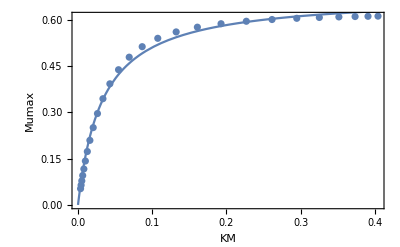

```mathematica
Show[ListPlot[tradeOffDataFerm, Frame-> True, FrameLabel->{"KM", "Mumax"}, BaseStyle->{"Arial",14}],Plot[tradeOffFitFerm[km], {km, 0,0.5}, Frame-> True, PlotRange->All]]
```

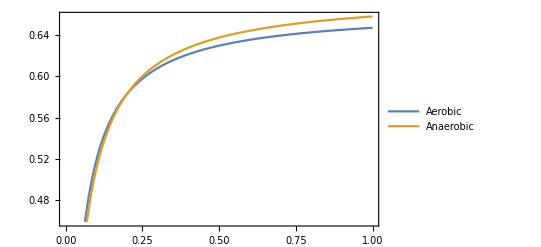

```mathematica
Plot[{tradeOffFit[km],tradeOffFitFerm[km]}, {km, 0,1}, Frame-> True, PlotLegends->{"Aerobic", "Anaerobic"}]
```